ClearAll

模拟参数: τ = 1/10, ki = 1, x0 = 5, T0 = 5, v0 = 1, k = 10

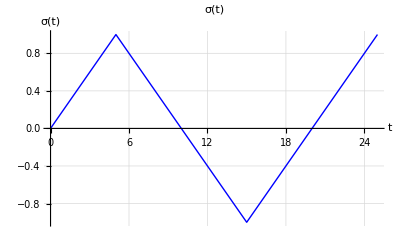

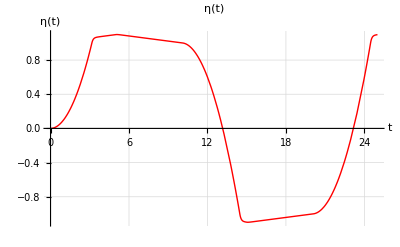

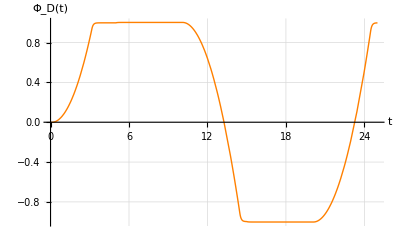

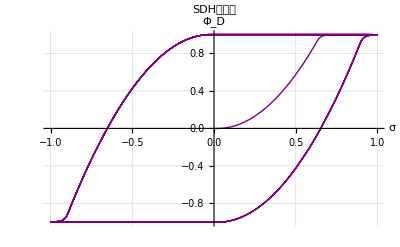

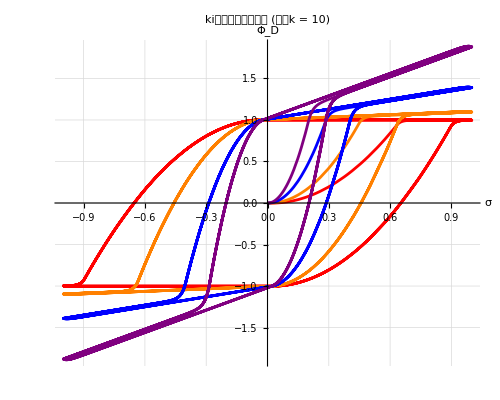

```mathematica
ClearAll
τ=1/10;          (*Dead zone斜率*)
ki=1;          (*积分系数*)
k=1/(τ ki);          (*k=1/(τ ki)*)
x0=5;          (*最大拉伸长度*)
T0=5;          (*半周期*)
v0=x0/T0;          (*等效拉动速度v0=x0/T0*)
F0=1;          (*阈值力*)

(*三角波输入*)
sigma[t_]:=TriangleWave[{-x0/T0,x0/T0},t/(4*T0)]
(*v0 T0 Sin[Pi/(2T0)t]*)

(*死区函数\Delta(\eta)*)
delta[eta_]:=Piecewise[{{1/(ki τ)*(eta-F0),eta>F0},{0,-F0<=eta<=F0},{1/(ki τ)*(eta+F0),eta<-F0}}]

(*SDH方程*)
equation=eta'[t]==ki*(sigma[t]-delta[eta[t]]);

(*初始条件*)
initialCondition=eta[0]==0;

(*数值求解微分方程*)
solution=NDSolve[{equation,initialCondition},eta,{t,0,15*T0},MaxSteps->10000,PrecisionGoal->8,AccuracyGoal->8];
etaFunc[t_]:=eta[t]/. solution[[1]];

(*SDH输出*)
phiD[t_]:=etaFunc[t]-(1/k)*sigma[t];
Print["模拟参数: τ = ",τ,", ki = ",ki,", x0 = ",x0,", T0 = ",T0,", v0 = ",v0,", k = ",k];

(*输入信号\sigma(t)*)
Plot[sigma[t],{t,0,5*T0},AxesLabel->{"t","σ(t)"},PlotLabel->"σ(t)",PlotStyle->{Blue,Thick},GridLines->Automatic,ImageSize->400]

(*状态反馈变量\eta(t)*)
Plot[etaFunc[t],{t,0,5*T0},AxesLabel->{"t","η(t)"},PlotLabel->"η(t)",PlotStyle->{Red,Thick},GridLines->Automatic,ImageSize->400]

(*输出变量\Phi_D(t)*)
Plot[phiD[t],{t,0,5*T0},AxesLabel->{"t","Φ_D(t)"},PlotStyle->{Orange,Thick},GridLines->Automatic,ImageSize->400]

(*滞回环*)
ParametricPlot[{sigma[t],phiD[t]},{t,0,15*T0},PlotLabel->"SDH滞回环",AxesLabel->{"σ","Φ_D"},PlotStyle->{Purple,Thick},AspectRatio->1/GoldenRatio,GridLines->Automatic,PlotRange->All,ImageSize->400]

(*不同ki值下的滞回环*)
plotHysteresisForDifferentKi[kVal_,v0Val_,T0Val_]:=Module[{kiValues={1,2,5,10},colors,plots,i},colors={Red,Orange,Blue,Purple};
plots=Table[ki=kiValues[[i]];
solution=NDSolve[{eta'[t]==ki*(sigma[t]-delta[eta[t]]),eta[0]==0},eta,{t,0,15*T0Val}];
etaFuncLocal[t_]:=eta[t]/. solution[[1]];
phiDLocal[t_]:=etaFuncLocal[t]-(1/kVal)*sigma[t];
ParametricPlot[{sigma[t],phiDLocal[t]},{t,0,15*T0Val},PlotStyle->colors[[i]]],{i,Length[kiValues]}];
Show[plots,PlotRange->All,GridLines->Automatic,ImageSize->500,AspectRatio->0.8,PlotLabel->"ki值对滞回环的影响 (参数k = "<>ToString[kVal]<>")",AxesLabel->{"σ","Φ_D"},PlotLegends->Placed[LineLegend[Table["ki = "<>ToString[kiValues[[i]]],{i,Length[kiValues]}],LegendLabel->Style["参数值",Bold,12]],{0.8,0.9}]]]

plotHysteresisForDifferentKi[k,v0,T0]
```

```mathematica
Export["/Users/huangyiding/Desktop/未命名.pdf",%464,"PDF"]
```

/Users/huangyiding/Desktop/未命名.pdf

```mathematica
Export["/Users/huangyiding/Desktop/未命名.pdf",%441,"PDF"]
```

/Users/huangyiding/Desktop/未命名.pdf

```mathematica
Export["/Users/huangyiding/Desktop/未命名.pdf",%286,"PDF"]
```

/Users/huangyiding/Desktop/未命名.pdf

```mathematica
Export["/Users/huangyiding/Desktop/Physics/BioPhysics Note/Hybrid Chain DRHC/Notes/Figure/Phi_D.pdf",%43,"PDF"]
```

/Users/huangyiding/Desktop/Physics/BioPhysics Note/Hybrid Chain DRHC/Notes/Figure/Phi_D.pdf

```mathematica
Export["/Users/huangyiding/Desktop/Physics/BioPhysics Note/Hybrid Chain DRHC/Notes/Figure/Phi_D.pdf",%19,"PDF"]
```

/Users/huangyiding/Desktop/Physics/BioPhysics Note/Hybrid Chain DRHC/Notes/Figure/Phi_D.pdf

```mathematica
Export["/Users/huangyiding/Desktop/未命名.pdf",%22,"PDF"]
```

/Users/huangyiding/Desktop/未命名.pdf

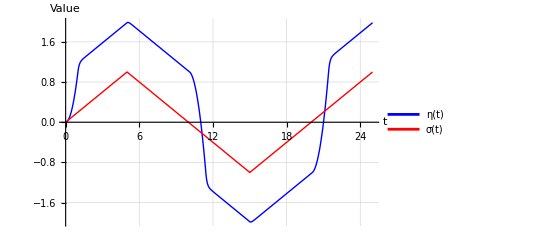

```mathematica
Plot[{etaFunc[t],sigma[t]},{t,0,5*T0},AxesLabel->{"t","Value"},PlotStyle->{{Blue,Thick},{Red,Thick}},GridLines->Automatic,ImageSize->400,(*新增图例*)PlotLegends->Placed[{"η(t)","σ(t)"},{0.8,0.9}  (*图例位置，可根据需要调整*)]]
```

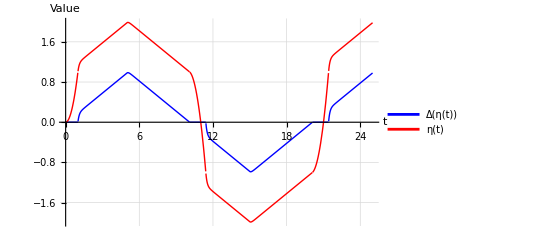

```mathematica
Plot[{delta[etaFunc[t]],etaFunc[t]},{t,0,5*T0},AxesLabel->{"t","Value"},PlotStyle->{{Blue,Thick},{Red,Thick}},GridLines->Automatic,ImageSize->400,(*新增图例*)PlotLegends->Placed[{"Δ(η(t))","η(t)"},{0.8,0.9}  (*图例位置，可根据需要调整*)]]
```

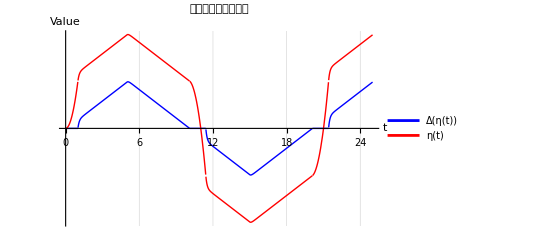

```mathematica
Show[%3514,Axes->True,Ticks->{Automatic,None}]
```